```mathematica
EqElast=
{Elast==mu (2 mu+3 lambda)/(mu+lambda),poisson==lambda/(2( mu + lambda))}
sollambda = Solve[EqElast,{mu,lambda}][[1]]
Elasticidade={Elast->25 10^9,poisson->0.25}
```

{Elast==(mu (3 lambda+2 mu))/(lambda+mu),poisson==lambda/(2 (lambda+mu))}

{lambda→-(Elast poisson)/((1+poisson) (-1+2 poisson)),mu→Elast/(2 (1+poisson))}

{Elast→25000000000,poisson→0.25}

```mathematica
Deform={
{(R-y)/R Cos[x/R]-1,-y/(2R) Sin[x/R],0},
{-y/(2R)Sin[x/R],Cos[x/R]-1,0},
{0,0,0}
}
TensorTensao=lambda Tr[Deform]IdentityMatrix[3]+2 mu Deform;
Energia=1/2 Tr[Deform.TensorTensao];
```

{{-1+((R-y) Cos[x/R])/R,-(y Sin[x/R])/(2 R),0},{-(y Sin[x/R])/(2 R),-1+Cos[x/R],0},{0,0,0}}

```mathematica
EnergiaFunc[R_]=Energia/.sollambda/.Elasticidade
EnergiaFunc[50]
```

1/2 ((-1+Cos[x/R]) (2.×10^10 (-1+Cos[x/R])+1.×10^10 (-2+Cos[x/R]+((R-y) Cos[x/R])/R))+(-1+((R-y) Cos[x/R])/R) (2.×10^10 (-1+((R-y) Cos[x/R])/R)+1.×10^10 (-2+Cos[x/R]+((R-y) Cos[x/R])/R))+(1.×10^10 y^2 Sin[x/R]^2)/R^2)

1/2 ((-1+Cos[x/50]) (2.×10^10 (-1+Cos[x/50])+1.×10^10 (-2+Cos[x/50]+1/50 (50-y) Cos[x/50]))+(-1+1/50 (50-y) Cos[x/50]) (2.×10^10 (-1+1/50 (50-y) Cos[x/50])+1.×10^10 (-2+Cos[x/50]+1/50 (50-y) Cos[x/50]))+4.×10^6 y^2 Sin[x/50]^2)

```mathematica
EnergiaVolume=Integrate[Energia/.sollambda/.Elasticidade,{y,-0.25,0.25},{z,-0.1,0.1},{x,-2.5,2.5}]//Chop
```

3.×10^10+(1.04167×10^8)/R^2-1.6×10^10 R Sin[2.5/R]+((1.04167×10^7)/R+2.×10^9 R) Sin[5./R]

```mathematica
EnergiaVolumeFunc[R_]=EnergiaVolume
```

3.×10^10+(1.04167×10^8)/R^2-1.6×10^10 R Sin[2.5/R]+((1.04167×10^7)/R+2.×10^9 R) Sin[5./R]

```mathematica
EnergiaFace[R_,Mz_]=-2Mz Sin[5/(2R)]
```

-2 Mz Sin[5/(2 R)]

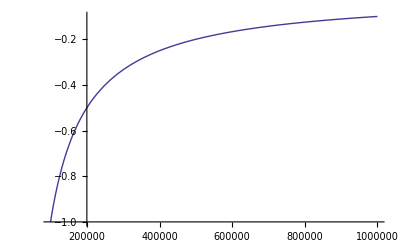

```mathematica
Plot[EnergiaFace[R,20000],{R,100000,1000000}]
```

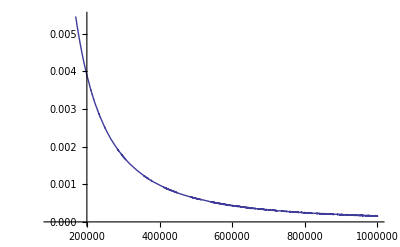

```mathematica
Plot[EnergiaVolumeFunc[R],{R,100000,1000000}]
```

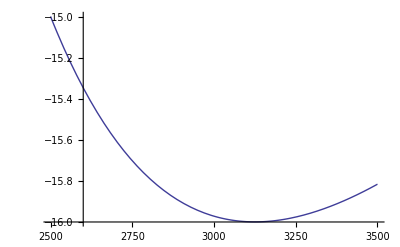

```mathematica
Plot[EnergiaVolumeFunc[R]+EnergiaFace[R,20000],{R,2500,3500}]
```

-(2.08333×10^8)/R^3+(4.×10^10 Cos[2.5/R])/R+(100000 Cos[5/(2 R)])/R^2-(5. ((1.04167×10^7)/R+2.×10^9 R) Cos[5./R])/R^2-1.6×10^10 Sin[2.5/R]+(2.×10^9-(1.04167×10^7)/R^2) Sin[5./R]

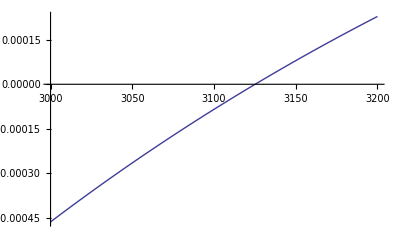

{R→3125.16}

```mathematica
DerivR[R_]=D[EnergiaVolumeFunc[R]+EnergiaFace[R,20000],{R}]
Plot[DerivR[R],{R,3000,3200}]
RSol=FindRoot[DerivR[R]==0,{R,3000}]
```

```mathematica
Approx=TensorTensao/.sollambda/.Elasticidade/.RSol
```

{{2.×10^10 (-1+0.000319984 (3125.16-y) Cos[0.000319984 x])+1.×10^10 (-2+Cos[0.000319984 x]+0.000319984 (3125.16-y) Cos[0.000319984 x]),-3.19984×10^6 y Sin[0.000319984 x],0},{-3.19984×10^6 y Sin[0.000319984 x],2.×10^10 (-1+Cos[0.000319984 x])+1.×10^10 (-2+Cos[0.000319984 x]+0.000319984 (3125.16-y) Cos[0.000319984 x]),0},{0,0,1.×10^10 (-2+Cos[0.000319984 x]+0.000319984 (3125.16-y) Cos[0.000319984 x])}}

```mathematica
Approx.{1,0,0}/.{x->2.5}
(Approx.{1,0,0}).{0,1,0}/.x->2.5
Integrate[Approx.{1,0,0}y/.x->2.5,{y,-0.25,0.25},{z,-0.1,0.1}]
Integrate[Approx.{1,0,0}/.x->2.5,{y,-0.25,0.25},{z,-0.1,0.1}]
```

{1.×10^10 (-1.+0.000319984 (3125.16-y))+2.×10^10 (-1+0.000319984 (3125.16-y)),-2559.74 y,0}

-2559.74 y

{-19999.,-5.33279,0}

{-1279.87,0.,0}

{-799959. Sin[0.000319984 x],2.×10^10 (-1+Cos[0.000319984 x])+1.×10^10 (-2+1.99992 Cos[0.000319984 x]),0}

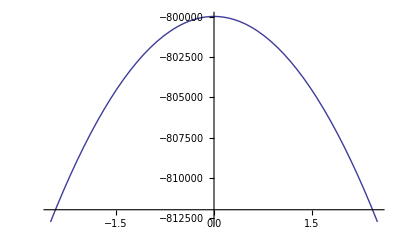

```mathematica
ForcasF2=Approx.{0,1,0}/.y->0.25
Plot[ForcasF2[[2]],{x,-2.5,2.5}]
```

{-3.19984×10^6 Sin[0.000319984 x]-2047.79 (3125.16-y) Sin[0.000319984 x]+1.×10^10 (-0.000319984 Sin[0.000319984 x]-1.0239×10^-7 (3125.16-y) Sin[0.000319984 x]),-3.19984×10^6 Cos[0.000319984 x]-1023.9 y Cos[0.000319984 x],0}

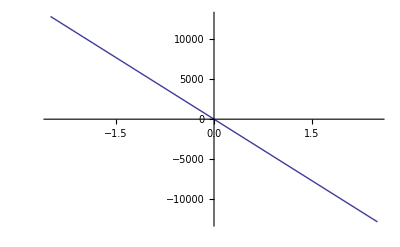

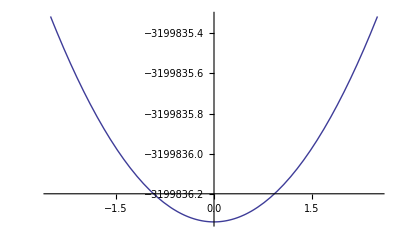

```mathematica
DivApprox=D[Approx[[1]],{x}]+D[Approx[[2]],y]+D[Approx[[3]],z]
Plot[DivApprox[[1]]/.y->0,{x,-2.5,2.5}]
Plot[DivApprox[[2]]/.y->0,{x,-2.5,2.5}]
```

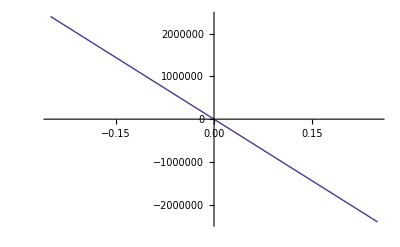

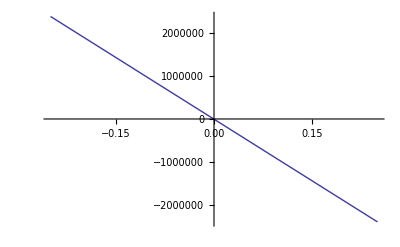

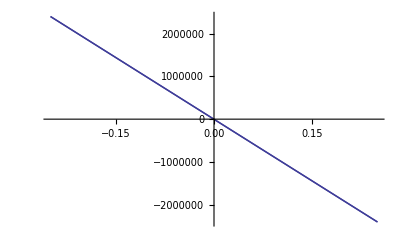

```mathematica
p1=Plot[(Approx.{1,0,0}).{1,0,0}/.x->0.5,{y,-0.25,0.25}]
p2=Plot[(Approx.{1,0,0}).{1,0,0}/.x->1.5,{y,-0.25,0.25}]
Show[p1,p2]
```